# § Percolation Theory Reveals Biophysics Properties of Virus-like Particles

This is the core code provided to reviewers of the above listed paper, allowing them to reproduce the primary results for the triangular tiling case.

A more thorough how-to guide will be published in a Wolfram Research-affiliated press release shortly after publication, but all basic elements associated with methodology verification are shown below.

	Nicholas Brunk - nbrunk@wolfram.com - nbrunk90@gmail.com - 2021.02.27

## § Initialization

Graph Definition

```mathematica
g1PariacotoVirus=
Module[{edgeList},
edgeList=(DeleteCases[{RowBox[{"1","<->","2"}],",",RowBox[{"1","<->","6"}],",",RowBox[{"1","<->","7"}],",",RowBox[{"2","<->","3"}],",",RowBox[{"2","<->","9"}],",",RowBox[{"3","<->","4"}],",",RowBox[{"3","<->","10"}],",",RowBox[{"4","<->","5"}],",",RowBox[{"4","<->","12"}],",",RowBox[{"5","<->","6"}],",",RowBox[{"5","<->","13"}],",",RowBox[{"6","<->","15"}],",",RowBox[{"7","<->","8"}],",",RowBox[{"7","<->","17"}],",",RowBox[{"8","<->","9"}],",",RowBox[{"8","<->","20"}],",",RowBox[{"9","<->","23"}],",",RowBox[{"10","<->","11"}],",",RowBox[{"10","<->","24"}],",",RowBox[{"11","<->","12"}],",",RowBox[{"11","<->","27"}],",",RowBox[{"12","<->","30"}],",",RowBox[{"13","<->","14"}],",",RowBox[{"13","<->","31"}],",",RowBox[{"14","<->","15"}],",",RowBox[{"14","<->","34"}],",",RowBox[{"15","<->","16"}],",",RowBox[{"16","<->","17"}],",",RowBox[{"16","<->","36"}],",",RowBox[{"17","<->","18"}],",",RowBox[{"18","<->","19"}],",",RowBox[{"18","<->","37"}],",",RowBox[{"19","<->","20"}],",",RowBox[{"19","<->","40"}],",",RowBox[{"20","<->","21"}],",",RowBox[{"21","<->","22"}],",",RowBox[{"21","<->","41"}],",",RowBox[{"22","<->","23"}],",",RowBox[{"22","<->","44"}],",",RowBox[{"23","<->","24"}],",",RowBox[{"24","<->","25"}],",",RowBox[{"25","<->","26"}],",",RowBox[{"25","<->","44"}],",",RowBox[{"26","<->","27"}],",",RowBox[{"26","<->","45"}],",",RowBox[{"27","<->","28"}],",",RowBox[{"28","<->","29"}],",",RowBox[{"28","<->","50"}],",",RowBox[{"29","<->","30"}],",",RowBox[{"29","<->","51"}],",",RowBox[{"30","<->","31"}],",",RowBox[{"31","<->","32"}],",",RowBox[{"32","<->","33"}],",",RowBox[{"32","<->","51"}],",",RowBox[{"33","<->","34"}],",",RowBox[{"33","<->","54"}],",",RowBox[{"34","<->","35"}],",",RowBox[{"35","<->","36"}],",",RowBox[{"35","<->","58"}],",",RowBox[{"36","<->","37"}],",",RowBox[{"37","<->","38"}],",",RowBox[{"38","<->","39"}],",",RowBox[{"38","<->","57"}],",",RowBox[{"39","<->","40"}],",",RowBox[{"39","<->","59"}],",",RowBox[{"40","<->","41"}],",",RowBox[{"41","<->","42"}],",",RowBox[{"42","<->","43"}],",",RowBox[{"42","<->","60"}],",",RowBox[{"43","<->","44"}],",",RowBox[{"43","<->","46"}],",",RowBox[{"45","<->","46"}],",",RowBox[{"45","<->","50"}],",",RowBox[{"46","<->","47"}],",",RowBox[{"47","<->","48"}],",",RowBox[{"47","<->","60"}],",",RowBox[{"48","<->","49"}],",",RowBox[{"48","<->","55"}],",",RowBox[{"49","<->","50"}],",",RowBox[{"49","<->","52"}],",",RowBox[{"51","<->","52"}],",",RowBox[{"52","<->","53"}],",",RowBox[{"53","<->","54"}],",",RowBox[{"53","<->","55"}],",",RowBox[{"54","<->","58"}],",",RowBox[{"55","<->","56"}],",",RowBox[{"56","<->","57"}],",",RowBox[{"56","<->","59"}],",",RowBox[{"57","<->","58"}],",",RowBox[{"59","<->","60"}]},","]/.RowBox[edgeParts_]:>edgeParts)/.{v1_,"<->",v2_}:>ToExpression[v1]<->ToExpression[v2];
Graph3D[edgeList]]
```

-Graphics3D-

Algorithm Code

```mathematica
(* Simple function to style text the way I like: *)
myStyle[text_,othOpts_:{}]:=Style[text,FontFamily->"Times",22,Black,othOpts]

(* An equivalent function that simply takes a specified input graph (γ), then removes (ϵ) random vertices: *)
holeyGraph[ϵ_,γ_]:=VertexDelete[γ,RandomSample[VertexList@γ,ϵ]]

(* A similar function that takes a specified input graph (γ), then removes (ϵ) random vertices: *)
edgeHoleyGraph[ϵ_,γ_]:=EdgeDelete[γ,RandomSample[EdgeList@γ,ϵ]]

	(* Implementation for stochastic equivalents (with a normally distributed number of vertices missing centered around a mean fraction (p): *)
	(* For vertices: *)
numVertsDel[p_,γ_]:=
Block[{v0=VertexCount[γ],initList=Range@VertexCount[γ]},	
finList={};	For[i=1,i≤v0,i++,If[RandomReal[{0,1.0}]<(1-p),AppendTo[finList,initList⟦i⟧],Null]];	Length@finList]

holeyGraphStoch[p_,γ_]:=VertexDelete[γ,RandomSample[VertexList[γ],numVertsDel[1-p,γ]]]

(* A function to Monte Carlo and return the fragmentation threshold: *)
assessPercolation[γ_,numReplicates_,ϵMin_:1,ϵMax_:"all"]:=
Block[{v0=VertexCount@γ,ϵMinReal=Round[ϵMin],ϵMaxReal=If[ϵMax=="all",Round[v0-v0/10],Round[ϵMax]],pMin=ϵMinReal/v0,pMax=ϵMaxReal/v0},
(* Collect the Monte Carlo assessment of the Subscript[P, con](ϵ) [probability the graph is connected as vertices are removed]: *)
percData=ParallelTable[{N[ϵ/v0],N@(1/numReplicates)Count[Table[ConnectedGraphQ@holeyGraph[ϵ,γ],numReplicates],True]},{ϵ,ϵMin,ϵMaxReal},Method->"CoarsestGrained"];
(* Generate smooth spline interpolations of the data: *)
pFunc=Interpolation[percData,Method->"Spline"];
(* Detect the percolation threshold as the point of steepest descent: *)
initGuess=First@First@Cases[SortBy[percData,Part[#,2]&],x_/;0.4<x⟦2⟧<0.6];
fragThresh=p/.FindRoot[pFunc[p]==0.5,{p,initGuess},MaxIterations->100000,Method->"Secant"]/.{fT_}:>fT;
(* Post-process a plot of the results: *)
percPlot=Show[
Plot[{pFunc[p]},{p,pMin,pMax},PlotRange->All,PlotLabel->myStyle["f_T = "<>ToString[fragThresh]],GridLines->{{fragThresh},{0.5}},PlotLegends->None],
ListPlot[percData]]]


(* A function to Monte Carlo and return the bond fragmentation threshold: *)
assessEdgePercolation[γ_,numReplicates_,ϵMin_:1,ϵMax_:"all"]:=
Block[{e0=EdgeCount@γ,ϵMaxReal=If[ϵMax=="all",Round[e0-e0/10],ϵMax],pMin=ϵMin/e0,pMax=ϵMaxReal/e0},
(* Collect the Monte Carlo assessment of the Subscript[P, con](ϵ) [probability the graph is connected as vertices are removed]: *)
edgePercData=ParallelTable[{N[ϵ/e0],N[1/numReplicates]*Count[Table[ConnectedGraphQ@edgeHoleyGraph[ϵ,γ],numReplicates],True]},{ϵ,ϵMin,ϵMaxReal},Method->"CoarsestGrained"];
(* Generate smooth spline interpolations of the data: *)
pFunc=Interpolation[edgePercData,Method->"Spline"];
(* Detect the percolation threshold as the point of steepest descent: *)
initGuess=First@First@Cases[SortBy[edgePercData,Part[#,2]&],x_/;0.4<x⟦2⟧<0.6];
edgePCThresh=p/.FindRoot[pFunc[p]==0.5,{p,initGuess},MaxIterations->100000,Method->"Secant"]/.{fT_}:>fT;
(* Post-process a plot of the results: *)
edgePercPlot=Show[
Plot[{pFunc[p]},{p,pMin,pMax},PlotRange->All,PlotLabel->myStyle["f_T^e = "<>ToString[edgePCThresh]],GridLines->{{edgePCThresh},{0.5}},PlotLegends->None],
ListPlot[edgePercData]]]
```

## § Fragmentation Threshold Reproduction

The following reproduces the fragmentation threshold of the triangular tiling (reported as f_T=0.226):

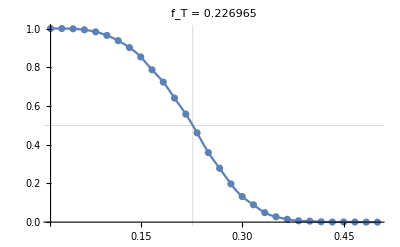
{51.3372,-Graphics-}

```mathematica
assessPercolation[g1PariacotoVirus,10000,1,Round[(VertexCount@g1PariacotoVirus)/2]]//AbsoluteTiming
```

Any discrepancy as you run this is due to the decreased number of Monte Carlo replicates used here (to allow it to evaluate in approximately a minute) relative to the much larger number of Monte Carlo replicates used in calculating the final result reported in the paper.

Reproduction of the edge fragmentation threshold of the triangular tiling is handled similarly (reported as f_T^e=0.208):

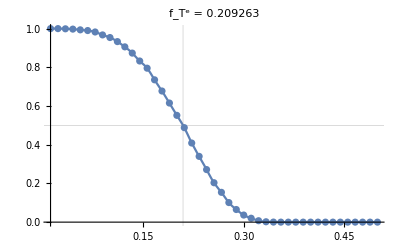
{71.0808,-Graphics-}

```mathematica
assessEdgePercolation[g1PariacotoVirus,10000,1,Round[(EdgeCount@g1PariacotoVirus)/2]]//AbsoluteTiming
```

Again, the same caveat applies for any approximation of the above result per-evaluation relative to the reported result of the paper:  the paper used more Monte Carlo replicates to converge on the reported value.

## § Fragmentation Product Distributions Reproduction

The following reproduces - for the same tiling - the fragment size distributions, associated PDF histogram, and the overlying CDF for four different values of the fraction of vertices deleted (p) roughly centered about the fragmentation threshold:

```mathematica
(* Data acquisition and empirical distribution generation: *)
sizeDistDataStochG1=Table[Flatten[ParallelTable[Length/@ConnectedComponents@holeyGraphStoch[p,g1PariacotoVirus],{10000},Method->"CoarsestGrained"],1],{p,{.1,.2,.3,.4}}];

sizeDistributionG1=EmpiricalDistribution/@sizeDistDataStochG1;
```

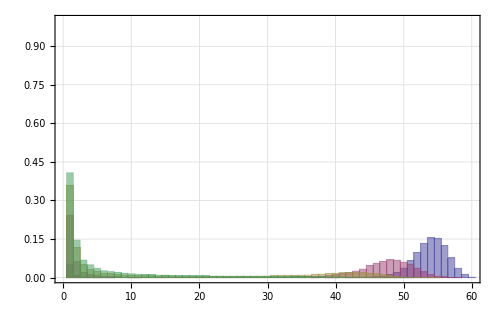

```mathematica
(* Final plotting: *)
With[{data=sizeDistDataStochG1,𝒟=sizeDistributionG1,subunitCount=VertexCount@g1PariacotoVirus},

With[{commOpts={PlotTheme->"Classic",PlotRange->{{0,subunitCount},{0,1}},Frame->True,FrameTicksStyle->Directive[FontFamily->"Times",16],ImageSize->500,GridLines->Automatic,GridLinesStyle->{#,#}&@{Dotted,Gray},PlotRangePadding->.055*{30*{1,1},{1,1}},ImagePadding->25,AspectRatio->1/GoldenRatio}},
Histogram[data,{1},"PDF",commOpts,
Epilog->Inset[DiscretePlot[Evaluate[CDF[#,x]&/@𝒟],{x,0,subunitCount},GridLines->None,FrameTicks->None,Joined->True,Filling->None,commOpts]]]]]
```